# Quantum Poly-spectra from Multiple Detectors

## MiniQuantumCatch For Multi-Detectors

## Defining Helper Functions

## Superoperators & Steady-State

First we calculate the Liouvillian Superoperator as a 2D matrix. This Liouvillian has n^2×n^2 elements. To calculate it, here we use the relation:
. The vectorized or flattened matrix is for example 
However, it is in our interest to redefine vectorizing in this way: 
This new way of vectorizing will spare of the headache will are going to suffer from ordering other matrices. Mathematically, the new way of vectorization work in the way that we first calculate the transposed matrix and then do the vectorization. The new equation would then look like the following:
 where  is a n^2×n^2 matrix called Commutation matrix (has nothing to do with commutator). The commutation matrix has the property: 
Rewriting it : 
Here I don’t provide any proof (But it can be found in my OneNote and later in obsidian) how to prove the following:



Here is  the damping operator while  is the measurement operator. The Liouvillian is then the sum of the three components.

### Commutation Matrix

```mathematica
KMatrix[m_,n_]:=Module[{positions,indices,commutationMatrix},
positions=Flatten[Table[{i+(j-1)*m,j+(i-1)*n},{i,m},{j,n}],1];
indices=SparseArray[positions->1,{m n,m n}];
commutationMatrix=Normal[indices];
Return[commutationMatrix];]
```

### Liouvillian

```mathematica
LiouvillianSuperoperator[Hamiltonian_,cOps_List,measureOps_List,γ_List,β_List]:=Module[{ℒ1,ℒ2,ℒ3,ℒ,Id,n,cOpsDagger,cOpsStar,measureOpsDagger,measureOpsStar,commutationMartix},
n=Length[Hamiltonian];
commutationMartix=KMatrix[n,n];
Id=IdentityMatrix[n];
cOpsDagger=Table[ConjugateTranspose[cOps[[k]]],{k,Length[cOps]}];
cOpsStar=Table[Conjugate[cOps[[k]]],{k,Length[cOps]}];
measureOpsDagger=Table[ConjugateTranspose[measureOps[[k]]],{k,Length[measureOps]}];
measureOpsStar=Table[Conjugate[measureOps[[k]]],{k,Length[measureOps]}];

ℒ1=ⅈ commutationMartix.(KroneckerProduct[Transpose[Hamiltonian],Id]-KroneckerProduct[Id,Hamiltonian]).commutationMartix;
ℒ2=Sum[γ[[k]] commutationMartix.KroneckerProduct[cOpsStar[[k]],cOps[[k]]],{k,Length[cOps]}].commutationMartix+Sum[(β[[k]])^2commutationMartix.KroneckerProduct[measureOpsStar[[k]],measureOps[[k]]].commutationMartix,{k,Length[measureOps]}];
ℒ3=Sum[
-γ[[k]]/2 commutationMartix.(KroneckerProduct[Id,cOpsDagger[[k]].cOps[[k]]]+KroneckerProduct[Transpose[cOps[[k]]].cOpsStar[[k]],Id]).commutationMartix,{k,Length[cOps]}]+Sum[-(β[[k]])^2/2 commutationMartix.(KroneckerProduct[Id,measureOpsDagger[[k]].measureOps[[k]]]+KroneckerProduct[Transpose[measureOps[[k]]].measureOpsStar[[k]],Id]).commutationMartix,{k,Length[measureOps]}];

ℒ=ℒ1+ℒ2+ℒ3;
Return[ℒ];]
```

### Steady-State

```mathematica
SteadyState[Hamiltonian_,Liouvillian_]:=Module[{n,evals,evecs,zeroIndex,ρSteady,ρtrace},n=Length[Hamiltonian];
evals=Eigenvalues[Liouvillian];
evecs=Eigenvectors[Liouvillian];
(*Zero is the largest since with damping all the others have negative real part*)
zeroIndex=Ordering[evals,-1][[1]];
ρSteady=evecs[[zeroIndex]];
ρtrace=Tr[ArrayReshape[ρSteady,{n,n}]];
ρSteady=ρSteady/ρtrace;
ρSteady=Partition[ρSteady,1];
Return[ρSteady];]
```

### 𝒜

The superoperator 𝒜 has the following definition:

we can show again that the superoperator 𝒜 can be calculated as:

```mathematica
Super𝒜[Hamiltonian_,measureOps_List,β_List]:=Module[{n,Id,measureOpsStar,𝒜,commutationMartix},
n=Length[Hamiltonian];
commutationMartix=KMatrix[n,n];
Id=IdentityMatrix[n];
measureOpsStar=Table[Conjugate[measureOps[[k]]],{k,Length[measureOps]}];
(*Enviromental damping has no influence, only measurement*)
𝒜=Table[(β[[k]])^2 /2commutationMartix.(KroneckerProduct[Id,measureOps[[k]]]+KroneckerProduct[measureOpsStar[[k]],Id]).commutationMartix,{k,Length[measureOps]}];
Return[𝒜];]
```

### 𝒜’

The modified 𝒜 superoperator is defined as:
 so we can calculate this modified superoperator as

```mathematica
Super𝒜Prim[Hamiltonian_,Liouvillian_,measureOps_List,β_List]:=Module[{n,m,Id,ρSteady,𝒜,𝒜DotρSteady,𝒜Prim},
n=Length[Hamiltonian];
m=Length[Liouvillian];
Id=IdentityMatrix[m];
ρSteady=SteadyState[Hamiltonian,Liouvillian];
𝒜=Super𝒜[Hamiltonian,measureOps,β];
𝒜DotρSteady=Table[𝒜[[k]].ρSteady,{k,Length[𝒜]}];
𝒜DotρSteady=Table[ArrayReshape[𝒜DotρSteady[[k]],{n,n}],{k,Length[𝒜]}];
𝒜Prim=Table[𝒜[[k]]-Id Tr[𝒜DotρSteady[[k]]],{k,Length[𝒜]}];
Return[𝒜Prim];]
```

## Fourier Transformation of The Propagator 𝒢’

Instead of calculating the propagator by calculating a matrix exponential, I can use the way introduced in prb2018:

To calculate Λ we just calculate the eigenvectors of the Liouvillian. (In Mathematica the results will be on row vectors. So we have to transpose so the vectors will be column shaped.)
The  containes the diagonal elements  for non steady-state. For the state-state we substitute the  with a 0.

```mathematica
DiagLiouvillian[Hamiltonian_,cOps_List,measureOps_List,γ_List,β_List]:=Module[{ℒ,Λ,λ,zeroIndex},
ℒ=LiouvillianSuperoperator[Hamiltonian,cOps,measureOps,γ,β];
Λ=Transpose[Eigenvectors[ℒ]];
λ=Eigenvalues[ℒ];
zeroIndex=Ordering[λ,-1][[1]];
Return[{Λ,λ,zeroIndex}];]
```

```mathematica
Gν[ν_, Λ_, λ_,zeroIndex_]:=Module[{DGTildePrimDiagElements,DGTildePrim,Gofν},
DGTildePrimDiagElements=1/(-λ-ⅈ ν);
DGTildePrimDiagElements=ReplacePart[DGTildePrimDiagElements,zeroIndex->0];
DGTildePrim=DiagonalMatrix[DGTildePrimDiagElements];
Gofν=Dot[Λ,DGTildePrim,Inverse[Λ]];
Return[Gofν];]
```

## Poly-spectra Functions

## S1

is the expectation value of the measurement and can be calculated as . The multiplication with is necessary to consider the measurement strength.

```mathematica
FirstOrderSpectrum[Hamiltonian_,Liouvillian_,measureOps_List,β_List]:=Module[{n,𝒜,ρSteady,𝒜DotρSteady,S1},
n=Length[Hamiltonian];
𝒜=Super𝒜[Hamiltonian,measureOps,β];
ρSteady=SteadyState[Hamiltonian,Liouvillian];
𝒜DotρSteady=Table[𝒜[[k]].ρSteady,{k,Length[𝒜]}];
𝒜DotρSteady=Table[ArrayReshape[𝒜DotρSteady[[k]],{n,n}],{k,Length[𝒜]}];
S1=Table[(β[[k]])^2Tr[𝒜DotρSteady[[k]]],{k,Length[𝒜]}];
Return[S1];]
```

## S2

is related the second order cumulant and can be described as follows:

```mathematica
SecondOrderSpectrum[ν_][Hamiltonian_,Liouvillian_,cOps_List,measureOps_List,γ_List,β_List]:=Module[{n,ρSteady,𝒜Prim,diagResults,S21,S22,S2},
n=Length[Hamiltonian];
ρSteady=SteadyState[Hamiltonian,Liouvillian];
𝒜Prim=Super𝒜Prim[Hamiltonian,Liouvillian,measureOps,β];
diagResults=DiagLiouvillian[Hamiltonian,cOps,measureOps,γ,β];
S21=ArrayReshape[𝒜Prim[[1]].Gν[ν,diagResults[[1]],diagResults[[2]],diagResults[[3]]].𝒜Prim[[2]].ρSteady,{n,n}];
S22=ArrayReshape[𝒜Prim[[2]].Gν[-ν,diagResults[[1]],diagResults[[2]],diagResults[[3]]].𝒜Prim[[1]].ρSteady,{n,n}];
S2=Product[β[[k]]^2,{k,Length[β]}](Tr[S21]+Tr[S22]);
Return[S2];]
```

## S3

```mathematica
ThirdOrderSpectrum[ν1_,ν2_][Hamiltonian_,Liouvillian_,cOps_List,measureOps_List,γ_List,β_List]:=Module[{n,νVector,νArguments,ρSteady,𝒜Prim,diagResults,perms,traces},
n=Length[Hamiltonian];
νVector={ν1,ν2,-ν1-ν2};
ρSteady=SteadyState[Hamiltonian,Liouvillian];
𝒜Prim=Super𝒜Prim[Hamiltonian,Liouvillian,measureOps,β];
diagResults=DiagLiouvillian[Hamiltonian,cOps,measureOps,γ,β];
perms=Permutations[{1,2,3}];

(*build the 6 contributions and sum their traces*)
traces=Table[With[{x=p[[1]],y=p[[2]],z=p[[3]]},Module[{tmp},tmp=𝒜Prim[[x]].Gν[νVector[[x]]+νVector[[y]],diagResults[[1]],diagResults[[2]],diagResults[[3]]].𝒜Prim[[z]].ρSteady;
tmp=𝒜Prim[[y]].Gν[νVector[[y]],diagResults[[1]],diagResults[[2]],diagResults[[3]]].tmp;
Tr@ArrayReshape[tmp,{n,n}]]],{p,perms}];

Total[traces]
]
```

## Calculations & Plotting

## Calculating Spectra

```mathematica
CalcSpectra[Hamiltonian_, cOps_List, measureOps_List, γ_List, β_List, orders_List]:=Module[{Liouvillian, spectrum=<||>},
Liouvillian=LiouvillianSuperoperator[Hamiltonian,cOps,measureOps,γ,β];
If[MemberQ[orders, 3],
spectrum["ThirdOrder"]=(Function[{ν1,ν2},Evaluate[ThirdOrderSpectrum[ν1,ν2][Hamiltonian,Liouvillian,cOps,measureOps,γ,β]]])
];
If[MemberQ[orders, 2],
spectrum["SecondOrder"]=(Function[{ν},Evaluate[SecondOrderSpectrum[ν][Hamiltonian,Liouvillian,cOps,measureOps,γ,β]]])
];
If[MemberQ[orders, 1],
spectrum["FirstOrder"]= (FirstOrderSpectrum[Hamiltonian,Liouvillian,measureOps,β])
];
spectrum
]
```

## Plotting Functions

```mathematica
seismicColors[x_?NumericQ]/;-1<=x<=1:=Blend[{RGBColor[0.,0.,0.3],RGBColor[0.,0.,1.],RGBColor[1.,1.,1.],RGBColor[1.,0.,0.],RGBColor[0.5,0.,0.]},x]
LinearGradientImage[seismicColors,{300,30}]
```

-Graphics-

```mathematica
PlotSpectra[spectrum_,orders_List,νMin_, νMax_,resolution_]:=Module[{thirdNummeric,maxAbs3,maxAbsIm3,colorFunc,colorFuncIm,realThird,imagThird, realSecond,imagSecond,plots={}},
If[MemberQ[orders, 3],
thirdNummeric=Table[spectrum["ThirdOrder"][ν1, ν2],{ν1,νMin,νMax,(νMax-νMin)/resolution},{ν2,νMin,νMax,(νMax-νMin)/resolution}];

maxAbs3=Max[Abs[Re[thirdNummeric]]];
maxAbsIm3=Max[Abs[Im[thirdNummeric]]];
colorFunc=Function[z,seismicColors[Rescale[z,{-maxAbs3,maxAbs3}]]];colorFuncIm=Function[z,seismicColors[Rescale[z,{-maxAbsIm3,maxAbsIm3}]]];

realThird=DensityPlot[Re[spectrum["ThirdOrder"][ν1,ν2]],{ν1,νMin,νMax},{ν2,νMin,νMax},ColorFunctionScaling->False,ColorFunction->colorFunc,PlotLegends->Placed[Automatic, Right],PlotPoints->resolution,MaxRecursion->8,PlotRange->All,PerformanceGoal->"Speed",PlotLabel->"Real Part of S3",ImageSize->Medium];imagThird=DensityPlot[Im[spectrum["ThirdOrder"][ν1,ν2]],{ν1,νMin,νMax},{ν2,νMin,νMax},ColorFunctionScaling->False,ColorFunction->colorFuncIm,PlotLegends->Placed[Automatic, Right],PlotPoints->resolution,MaxRecursion->8,PlotRange->All,PerformanceGoal->"Speed",PlotLabel->"Imaginary Part of S3",ImageSize->Medium];
AppendTo[plots,GraphicsRow[{realThird,imagThird}]]
];
If[MemberQ[orders, 2],
realSecond=Plot[Re[spectrum["SecondOrder"][ν]],{ν,νMin,νMax},PlotPoints->resolution,MaxRecursion->2,PlotRange->All,PerformanceGoal->"Speed",PlotLabel->"Real Part of S2"];
imagSecond=Plot[Im[spectrum["SecondOrder"][ν]],{ν,νMin,νMax},PlotPoints->resolution,MaxRecursion->2,PlotRange->All,PerformanceGoal->"Speed",PlotLabel->"Imaginary Part of S2"];
AppendTo[plots,GraphicsRow[{realSecond,imagSecond}]]
];
If[MemberQ[orders,1],Print["First-order spectrum (S1):"];
Print[spectrum["FirstOrder"]];];

If[Length[plots]>0,GraphicsGrid[Partition[plots,1]]]
]
```

## Example

Let’s imagine an electron in a magnetic field . For such a system we can write the Hamiltonian as . In such a system, the electron spin will rotate in the plane of x-y. The second order cross spectrum of x-y is then 
We know  
and 
Let’s assume that the initial condition is that the electron spin is pointing the same direction as . Such rotation will be Cosine function. Since it the spin rotates towards the  direction we have:

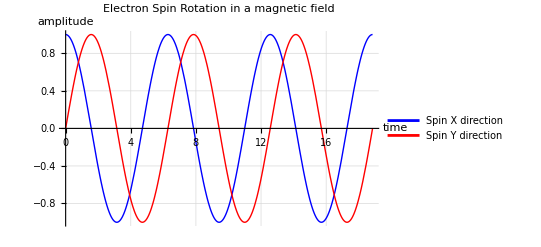

Meaning that we can substitute  with  where  is the time of one period. then:

Yielding 
So we expect  and purely imaginary with no real part.

```mathematica
HamiltonainExample=PauliMatrix[3]/2+ PauliMatrix[1]/2;
cOpsListExample={{{0,0},{1,0}}*0.5};
measureOpsListExample={PauliMatrix[1]/2,PauliMatrix[2]/2};
γListExample={1};
βListExample={0.01,0.01};
SecondOrderCrossExample=CalcSpectra[HamiltonainExample, cOpsListExample, measureOpsListExample, γListExample, βListExample, {2}];
PlotSpectra[SecondOrderCrossExample,{2},0, 3,170]
```

-Graphics-

As we see the imaginary part is giving the correct phase information and correlation between the two spins. The constant 0 for the real part was also expected.

## Examining different Systems

```mathematica
cOpsListExample={{{0,0},{1,0}}*0.5};
measureOpsListExample={PauliMatrix[2]/2,PauliMatrix[2]/2, PauliMatrix[2]/2};
γListExample={1};
βListExample={0.01,0.01, 0.01};
ThirdOrderCrossExample=CalcSpectra[HamiltonainExample, cOpsListExample, measureOpsListExample, γListExample, βListExample, {3}];
```

```mathematica
PlotSpectra[ThirdOrderCrossExample,{3},-3, 3,50]
```

-Graphics-

## Coupled Electron-Nucleon System

### Defining Operators and Modelling

```mathematica
dim[j_]:=2 j+1;
Jz[j_]:=-DiagonalMatrix[Table[m,{m,-j,j}]];
Jplus[j_]:=Module[{d=dim[j]},Table[If[i==k+1,With[{m=k-(j+1)},Sqrt[(j-m) (j+m+1)]],0],{i,d},{k,d}]];
Jminus[j_]:=ConjugateTranspose[Jplus[j]];
Jx[j_]:=(Jplus[j]+Jminus[j])/2;
Jy[j_]:=-(Jplus[j]-Jminus[j])/(2 I);
```

```mathematica
j=1;
nNStates=dim[j];
nEStates=dim[1/2];
```

```mathematica
hbar=6.582 10^-4;
h=2*Pi*hbar;
```

```mathematica
A=100.2 10^-6*h;
P=1.27 10^-6*h;
βgE=0.172*hbar;
βgN=9.329 10^-6*hbar;
(*Electron*)
sxE=Jx[1/2];
syE=Jy[1/2];
szE=Jz[1/2];
sE = {sxE,syE,szE};

(*Nucleon*)
sxN=Jx[j];
syN=Jy[j];
szN=Jz[j];
sN = {sxN,syN,szN};
(*Magnetic Field*)
b0=0.05;
B=b0{1,0,0};
```

```mathematica
H=βgE*KroneckerProduct[Sum[B[[i]] sE[[i]],{i,1,Length[B]}],IdentityMatrix[nNStates]]+A*Sum[KroneckerProduct[sE[[i]],sN[[i]]],{i,1,Length[sE]}]+P*KroneckerProduct[IdentityMatrix[nEStates],(szN)^2]-βgN*KroneckerProduct[IdentityMatrix[nEStates],Sum[B[[i]] sN[[i]],{i,1,Length[B]}]];
H=H/hbar;
N[H]//TraditionalForm
```

(0.000322767+0. ⅈ | -3.2983×10^-7+0. ⅈ | 0.+0. ⅈ | 0.0043+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-3.2983×10^-7+0. ⅈ | 0.+0. ⅈ | -3.2983×10^-7+0. ⅈ | 0.000445177+0. ⅈ | 0.0043+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -3.2983×10^-7+0. ⅈ | -0.000306808+0. ⅈ | 0.+0. ⅈ | 0.000445177+0. ⅈ | 0.0043+0. ⅈ
0.0043+0. ⅈ | 0.000445177+0. ⅈ | 0.+0. ⅈ | -0.000306808+0. ⅈ | -3.2983×10^-7+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.0043+0. ⅈ | 0.000445177+0. ⅈ | -3.2983×10^-7+0. ⅈ | 0.+0. ⅈ | -3.2983×10^-7+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.0043+0. ⅈ | 0.+0. ⅈ | -3.2983×10^-7+0. ⅈ | 0.000322767+0. ⅈ)

```mathematica
cops1=KroneckerProduct[IdentityMatrix[2],szN];
cops2=KroneckerProduct[szE,IdentityMatrix[3]];
cOpsList1={cops1,cops2};
```

```mathematica
measureops1=KroneckerProduct[IdentityMatrix[2],sxN];
measureops2=KroneckerProduct[szE,IdentityMatrix[3]];
measureOpsList1={measureops1,measureops2,measureops2};
```

```mathematica
γ1=5 10^-4;
γ2=2 10^-2;
γList1={γ1,γ2};
β1=10^-2;
βList1={β1,β1, β1};
```

```mathematica
CrossSpectrum1=CalcSpectra[H, cOpsList1, measureOpsList1, γList1, βList1, {3}];
```

```mathematica
PlotSpectra[CrossSpectrum1,{3},0, 0.005,5]
```

```mathematica
Re[Expand[CrossSpectrum1]]
```